# Tangent Space

## Environment

```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],CellContext->Notebook];
Off[Solve::ifun];
```

## Boxes

```mathematica
MakeBoxes[a3,StandardForm]:=SubscriptBox["a","3"];
MakeExpression[SubscriptBox["a","3"],StandardForm]:=MakeExpression["a3",StandardForm];
MakeBoxes[c3,StandardForm]:=SubscriptBox["c","3"];
MakeExpression[SubscriptBox["c","3"],StandardForm]:=MakeExpression["c3",StandardForm];
MakeBoxes[dtB,StandardForm]:=SuperscriptBox["dt","B"];
MakeExpression[SuperscriptBox["dt","B"],StandardForm]:=MakeExpression["dtB",StandardForm];
MakeBoxes[dtG,StandardForm]:=SuperscriptBox["dt","G"];
MakeExpression[SuperscriptBox["dt","G"],StandardForm]:=MakeExpression["dtG",StandardForm];
MakeBoxes[dtR,StandardForm]:=SuperscriptBox["dt","R"];
MakeExpression[SuperscriptBox["dt","R"],StandardForm]:=MakeExpression["dtR",StandardForm];
MakeBoxes[ds2,StandardForm]:=SuperscriptBox["ds","2"];
MakeExpression[SuperscriptBox["ds","2"],StandardForm]:=MakeExpression["ds2",StandardForm];
MakeBoxes[dxC,StandardForm]:=SuperscriptBox["dx","C"];
MakeExpression[SuperscriptBox["dx","C"],StandardForm]:=MakeExpression["dxC",StandardForm];
MakeBoxes[dxM,StandardForm]:=SuperscriptBox["dx","M"];
MakeExpression[SuperscriptBox["dx","M"],StandardForm]:=MakeExpression["dxM",StandardForm];
MakeBoxes[dxtM,StandardForm]:=SubsuperscriptBox["dx","t","M"];
MakeExpression[SubsuperscriptBox["dx","t","M"],StandardForm]:=MakeExpression["dxtM",StandardForm];
MakeBoxes[dxtY,StandardForm]:=SubsuperscriptBox["dx","t","Y"];
MakeExpression[SubsuperscriptBox["dx","t","Y"],StandardForm]:=MakeExpression["dxtY",StandardForm];
MakeBoxes[dxY,StandardForm]:=SuperscriptBox["dx","Y"];
MakeExpression[SuperscriptBox["dx","Y"],StandardForm]:=MakeExpression["dxY",StandardForm];
MakeBoxes[dxyM,StandardForm]:=SubsuperscriptBox["dx","y","M"];
MakeExpression[SubsuperscriptBox["dx","y","M"],StandardForm]:=MakeExpression["dxyM",StandardForm];
MakeBoxes[dxyY,StandardForm]:=SubsuperscriptBox["dx","y","Y"];
MakeExpression[SubsuperscriptBox["dx","y","Y"],StandardForm]:=MakeExpression["dxyY",StandardForm];
MakeBoxes[dyM,StandardForm]:=SuperscriptBox["dy","M"];
MakeExpression[SuperscriptBox["dy","M"],StandardForm]:=MakeExpression["dyM",StandardForm];
MakeBoxes[dyY,StandardForm]:=SuperscriptBox["dy","Y"];
MakeExpression[SuperscriptBox["dy","Y"],StandardForm]:=MakeExpression["dyY",StandardForm];
MakeBoxes[gμν,StandardForm]:=SubscriptBox["g","μν"];
MakeExpression[SubscriptBox["g","μν"],StandardForm]:=MakeExpression["gμν",StandardForm];
MakeBoxes[properSpace,StandardForm]:=SuperscriptBox["x","′"];
MakeExpression[SuperscriptBox["x","′"],StandardForm]:=MakeExpression["properSpace",StandardForm];
MakeBoxes[properTime,StandardForm]:=SuperscriptBox["t","′"];
MakeExpression[SuperscriptBox["t","′"],StandardForm]:=MakeExpression["properTime",StandardForm];
MakeBoxes[t0,StandardForm]:=SubscriptBox["t","0"];
MakeExpression[SubscriptBox["t","0"],StandardForm]:=MakeExpression["t0",StandardForm];
MakeBoxes[tB,StandardForm]:=SuperscriptBox["t","B"];
MakeExpression[SuperscriptBox["t","B"],StandardForm]:=MakeExpression["tB",StandardForm];
MakeBoxes[tG,StandardForm]:=SuperscriptBox["t","G"];
MakeExpression[SuperscriptBox["t","G"],StandardForm]:=MakeExpression["tG",StandardForm];
MakeBoxes[tR,StandardForm]:=SuperscriptBox["t","R"];
MakeExpression[SuperscriptBox["t","R"],StandardForm]:=MakeExpression["tR",StandardForm];
MakeBoxes[Vt,StandardForm]:=SubscriptBox["V","t"];
MakeExpression[SubscriptBox["V","t"],StandardForm]:=MakeExpression["Vt",StandardForm];
MakeBoxes[xM,StandardForm]:=SuperscriptBox["x","M"];
MakeExpression[SuperscriptBox["x","M"],StandardForm]:=MakeExpression["xM",StandardForm];
MakeBoxes[Xt,StandardForm]:=SubscriptBox["X","t"];
MakeExpression[SubscriptBox["X","t"],StandardForm]:=MakeExpression["Xt",StandardForm];
MakeBoxes[xY,StandardForm]:=SuperscriptBox["x","Y"];
MakeExpression[SuperscriptBox["x","Y"],StandardForm]:=MakeExpression["xY",StandardForm];
MakeBoxes[yM,StandardForm]:=SuperscriptBox["y","M"];
MakeExpression[SuperscriptBox["y","M"],StandardForm]:=MakeExpression["yM",StandardForm];
MakeBoxes[θM,StandardForm]:=SuperscriptBox["θ","M"];
MakeExpression[SuperscriptBox["θ","M"],StandardForm]:=MakeExpression["θM",StandardForm];
MakeBoxes[θY,StandardForm]:=SuperscriptBox["θ","Y"];
MakeExpression[SuperscriptBox["θ","Y"],StandardForm]:=MakeExpression["θY",StandardForm];
```

## Units

```mathematica
s=1;
m=1;
cm=0.01 m;
kg=1;
g=0.001 kg;
J=(kg m^2)/s^2;
K=1;
km=1000 m;
yr=60 60 24 365.25 s;
kyr=1000 yr;
Myr=1000 kyr;
Gyr=1000 Myr;
pc=3.08567758 10^13 km;
kpc=1000 pc;
Mpc=1000 kpc;
Gpc=1000 Mpc;
```

## Constants

```mathematica
G=6.67408 10^-11 m^3/(kg s^2);
ℏ=6.62607004 10^-34 J s;
Subscript[k, B]=1.380649 10^-23 J/K;
Subscript[a, B]=(8 π^5 Subscript[k, B]^4)/(15 ℏ^3 Subscript[c, 3]^3)J/(m^3 K^4);
Subscript[η, 0]=Subscript[η, t][Subscript[t, 0]];
h=2/(100 Subscript[t, 0])Mpc/km;
Subscript[H, 0]=h 100 km/(s Mpc);
Subscript[T, 0]=2.7255 K;
θ100=1.0411;
Subscript[A, He]=0.25;
Subscript[A, H]=0.75;
Subscript[m, He]=6.6464764 10^-27 kg;
Subscript[m, H]=1.6735575 10^-27 kg;
Subscript[σ, T]=6.6524 10^-29 m^2;
Subscript[ρ, γ]=(Subscript[a, B] Subscript[T, 0]^4)/Subscript[c, 3]^2 kg/m^3;
```

## Clear Variables

```mathematica
ClearAll[dt^R,dt^B,dx^M,dx^Y,v,θ,Subscript[a, 3],Subscript[c, 3],t,Subscript[t, 0]]
```

## The metric tensor (with the assumption of simultaneity)

```mathematica
Subscript[g, μν]=Limit[({{-(Subscript[c, 3]+Subscript[a, 3] Subscript[t, 0])^2, 0, 0, 0}, {0, ((Subscript[t, 0]^2+Subscript[t, 1]^2)^2)/(4 Subscript[t, 0]^4), 0, 0}, {0, 0, ((Subscript[t, 0]^2+Subscript[t, 1]^2)^2)/(4 Subscript[t, 0]^4), 0}, {0, 0, 0, ((Subscript[t, 0]^2+Subscript[t, 1]^2)^2)/(4 Subscript[t, 0]^4)}}),{t0->t,Subscript[t, 1]->t}];
Subscript[g, μν]//MatrixForm
```

(-(c_3+a_3 t)^2 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

### Some definitions

```mathematica
dt^R=dt^R/.Solve[dt^R/dt^B==Cos[θ],dt^R][[1]]
```

dt^B Cos[θ]

### The Tangent Space

```mathematica
Subscript[V, t]=-ⅈ(∫Subscript[a, 3] ⅆt+Subscript[c, 3]);
Subscript[X, t]=0;
```

### The tangent vector is the sum of the time and space components.

```mathematica
dx^M=dx^M/.FullSimplify[Solve[Subscript[V, t]^2==Subscript[g, μν][[1,1]](dt^B/dt^R)^2+Subscript[g, μν][[2,2]](dx^M/dt^R)^2,dx^M]][[2]]
```

dt^B (c_3+a_3 t) Cos[θ] √(Tan[θ]^2)

### The angle between time axes is a function of relative velocity.

```mathematica
θ=θ/.Solve[dx^M/(ⅈ dt^B)==-ⅈ v,θ][[1]]
```

ArcSin[v/(c_3+a_3 t)]

### Coordinate time vs. Proper Time

```mathematica
ClearAll[dt^R,dx^M]
```

```mathematica
dt^B=dt^R Sec[θ]
```

dt^R/(√(1-v^2/(c_3+a_3 t)^2))

### Coordinate space vs Proper Space

```mathematica
dx^M=dx^M/.FullSimplify[Solve[Subscript[X, t]==Subscript[g, μν][[1,1]](dt^B/dx^Y)^2+Subscript[g, μν][[2,2]](dx^M/dx^Y)^2/.{dt^R->dx^Y/(ⅈ(Subscript[c, 3]+Subscript[a, 3] t))},dx^M],{(Subscript[c, 3]+Subscript[a, 3] t)^2-v^2>0}]⟦2⟧
```

(ⅈ dx^Y (c_3+a_3 t))/(√((c_3+a_3 t)^2-v^2))

### Proper Time and Space vs . Velocity

```mathematica
Subscript[c, 3]=2.663617×10^8 m/s;
Subscript[a, 3]=3.4630912×10^-11 m/s^2;
t=9.653442×10^17 s;
```

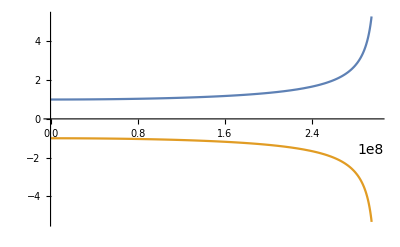

```mathematica
Plot[{dt^B/.dt^R->1,ⅈ dx^M/.dx^Y->1},{v,0,(Subscript[c, 3]+Subscript[a, 3] t)}]
```

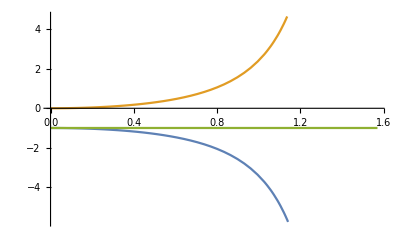

```mathematica
Plot[{-Sec[θ]^2,Tan[θ]^2,-Sec[θ]^2+Tan[θ]^2},{θ,0,π/2}]
```